# Computational Framework for Jefimenko’s Equations Tripp Henderson, PHGN462, Dec. 17, 2025

This document discusses and briefly tests an early framework for directly evaluating Jefimenko’s equations, with the most interesting and furthest discussed test case being the evaluation of near E fields produced by a moving, “fuzzy” cube of uniform, positive charge density. Within this framework, E and B fields are defined per-term, with the intention of allowing the user to investigate the fields from a charge from a single “source” term exclusively. For example, the E field produced by the “rho dot” term for a moving “fuzzy” cube is evaluated and plotted independently of “rho” and “J dot.” Suspected issues are also discussed.

The intended architecture for these evaluations was to perform primarily symbolic computation for derivative terms (e.g. dERho) until the final computation step—typically numerically integrating several times to produce a plot. Please note, the code in this document is also fairly computationally heavy for a personal computer—or mine, at least. If you’re running a cell, consider finding something to do for the next 3-5 minutes.

#### Set Up

This is a self explanatory set up of terms designed to help symbolically compute derivative terms. Because of the symbolic emphasis, “=” is used fairly frequently instead of “:=”. Note that universally, “rs” relates to source coordinates, while “r” relates to the coordinates of fields.

```mathematica
Clear["Global'*"] 
(*Set Up*) 
	(*Constants*)
	 c=3*^8;
	eps0=9*^-12;
	mu=4 Pi*10^-7;
	(*Displacement & Retardation*)
	R=Norm[r-rs]; 
	RVec=r-rs;
	RHat=RVec/R;
	tr=t-R/c;
	(*Vectors*)
	rs={rsx,rsy,rsz}; (*These show up in definitions like rho; often just a shortcut*)
	r={rx,ry,rz};
	(*Helpers*)
	smoothStep[x_]=1/2 (1+Tanh[x/0.25]);
	 (*dE field,seperated by term*) 
	dEFromRho:=(1/(4 Pi eps0))*
	(RHat/R^2)*
	(rho[rsx,rsy,rsz,tr]);
	dEFromRhoDot:=(1/(4 Pi eps0))*
	(RHat/R/c)*
	(rhoDot[rsx,rsy,rsz,tr]);
	dEFromJDot:=(1/(4 Pi eps0))*
	(1/R/c^2)*
	(JDot[rsx,rsy,rsz,tr]);
	(*dB field,seperated by term*)(*Not used,too computationally intensitve*)
	dBFromJ:=(mu/(4 Pi))*
	(1/R^2)*
	(J[rsx,rsy,rsz,tr]);
	dBFromJDot:=
	(mu/(4 Pi))*
	(1/R/c)*
	(JDot[rsx,rsy,rsz,tr]);
```

#### Stationary Cube

This is the first test case. We define rho with boolean functions, define dERho symbolically, prepare a function to integrate over dERho for a specific point, and then graph numerous points. An independent region plot was used to visualize the cube itself, since plot functions like DensityPlot are not compatible with boolean arguments.

```mathematica
(*Motionless Cube of Positive Charge*) 
	Clear[rho,dERho,ERho,rhoPlot,ERhoPlot,rhoPlot3D,ERhoPlot3D];
	(*Define Case*)
		rho[rsx_,rsy_,rsz_,t_]=
		Boole[rs[[1]]<1&&rs[[1]]>-1&&rs[[2]]<1&&rs[[2]]>-1&&rs[[3]]<1&&rs[[3]]>-1];
	(*Evaluate*)
		dERho[rsx_,rsy_,rsz_,rx_,ry_,rz_]=dEFromRho/.t->0;
		ERho[rx_,ry_,rz_]:=
		NIntegrate[dERho[rsx,rsy,rsz,rx,ry,rz],{rsx,-1,1},{rsy,-1,1},{rsz,-1,1}]; 
	(*Graph 3D - rho*)
		rhoPlot3D=
		RegionPlot3D[x<1&&x>-1&&y<1&&y>-1&&z<1&&z>-1,{x,-4,4},
		{y,-4,4},{z,-4,4},PlotPoints->50,Mesh->None,
		PlotStyle->Directive[Red,Opacity[0.4]]];
	(*Graph 3D - E from rho*)
		ERhoPlot3D=
		VectorPlot3D[ERho[rx,ry,rz],{rx,-4,4},{ry,-4,4},{rz,-4,4},VectorPoints->4];
	Show[rhoPlot3D,ERhoPlot3D]
```

-Graphics3D-

The resulting plot seems satisfactory.

#### Stationary Sphere

This test case is nearly identical to the last. I felt interested in a sphere because, as I imagine, I could try taking the limit of the E field as the radius of the sphere approaches 0, instead producing a point. I don’t expect this to be the case for a cube.

```mathematica
(*Motionless Sphere of Positive Charge*)
	Clear[rho,dERho,ERho,rhoPlot3D,ERhoPlot3D];
	(*Define Case*)
		rho[rsx_,rsy_,rsz_,t_]=
		Boole[rs[[1]]^2+rs[[2]]^2+rs[[3]]^2<1];
	(*Evaluate*)
		dERho[rsx_,rsy_,rsz_,rx_,ry_,rz_]=dEFromRho/.t->0;
		ERho[rx_,ry_,rz_]:=
		NIntegrate[dERho[rsx,rsy,rsz,rx,ry,rz],{rsx,-1,1},{rsy,-1,1},{rsz,-1,1}]; 
	(*Graph 3D - rho*)
		rhoPlot3D=
		RegionPlot3D[x^2+y^2+z^2<1,{x,-4,4},
		{y,-4,4},{z,-4,4},PlotPoints->25,Mesh->None,
		PlotStyle->Directive[Red,Opacity[0.4]]];
	(*Graph 3D - E from rho*)
		ERhoPlot3D=
		VectorPlot3D[ERho[rx,ry,rz],{rx,-4,4},{ry,-4,4},{rz,-4,4},VectorPoints->4];
	Show[rhoPlot3D,ERhoPlot3D]
```

-Graphics3D-

#### Fuzzy, Moving Cube

This is the intended flagship test-case of the framework so far. The cube is made “fuzzy,” so that when it moves,  Rho and J are numerically differentiable over time without converging. In my opinion, “fuzziness” does not seem problematic for application. A fuzzy cube, shrunk towards 0, should act like a cubic-point, so fuzziness should maintain potential for point-like-ness.

The rho dot and J dot terms are also explicitly defined in this case—rho dot trivially, by taking the time derivative, and J dot by deducing that any current density flows in the direction of the cube’s velocity, and then differentiating, actually producing a similar expression to rho dot.

Computation for this case becomes especially intensive, potentially from the non-boolean rho expression. Integration is done around most of the fuzzy cube ( e.g. “{rsx, -1.5,1.5}” ), the precision goal is reduced, and exclusions are used to avoid detected divergence during the divergence process, presumably due to terms moving too close to 0 in the denominator of dEFromRho, dEFromRhoDot, etc.. However, why cases where rsx approximately equals rx, but rsy and sy are not approximately equal, throw convergence errors is not clear to me given the structure of dEFromRho.

ContourPlot and VectorPlot (both 2D) are used to better visualize smaller differences, like the gap in rhoDot.

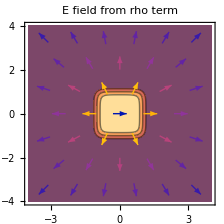

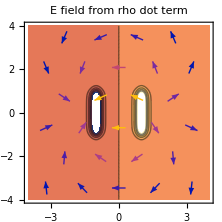

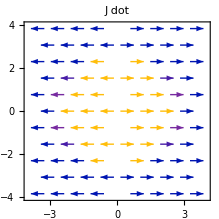

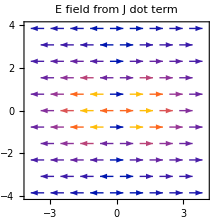

```mathematica
(*Fuzzy Moving Cube of Positive Charge*)
Clear[t,rho,rhoDot,JDot,dERho,ERho,dERhoDot,ERhoDot,dEJDot,EJDot,rhoPlot,rhoDotPlot,ERhoPlot,ERhoDotPlot];
	(*Define Case*)
		rho[rsx_,rsy_,rsz_,t_]=
		smoothStep[rs[[1]]+1-t] smoothStep[1-rs[[1]]+t] smoothStep[rs[[2]]+1] *
		smoothStep[1-rs[[2]]] smoothStep[1-rs[[3]]] smoothStep[1-rs[[3]]];
		rhoDot[rsx_,rsy_,rsz_,t_]=D[rho[rsx,rsy,rsz,t],t];
		JDot[rsx_,rsy_,rsz_,t_]={D[rho[rsx,rsy,rsz,t],t],0};
	(*Evaluate*)
		dERho[rsx_,rsy_,rsz_,rx_,ry_]=
		(dEFromRho/.rz->0/.t->0 )[[{1,2}]];
		ERho[rx_,ry_]:=
		NIntegrate[dERho[rsx,rsy,rsz,rx,ry],{rsx,-1.5,1.5},
		{rsy,-1.5,1.5},{rsz,-1.5,1.5},Exclusions->{rsx==rx,rsy==ry},PrecisionGoal->2];
		dERhoDot[rsx_,rsy_,rsz_,rx_,ry_]=
		(dEFromRhoDot/.rz->0/.t->0)[[{1,2}]];
		ERhoDot[rx_,ry_]:=
		NIntegrate[dERhoDot[rsx,rsy,rsz,rx,ry],{rsx,-1.5,1.5},
		{rsy,-1.5,1.5},{rsz,-1.5,1.5},Exclusions->{rsx==rx,rsy==ry},PrecisionGoal->2];
		dEJDot[rsx_,rsy_,rsz_,rx_,ry_]=
		(dEFromJDot/.rz->0/.t->0)[[{1,2}]];
		EJDot[rx_,ry_]:=
		NIntegrate[dEJDot[rsx,rsy,rsz,rx,ry],{rsx,-1.5,1.5},
		{rsy,-1.5,1.5},{rsz,-1.5,1.5},Exclusions->{rsx==rx,rsy==ry},PrecisionGoal->2];
	(*Graph-rho*)
		rhoPlot=
		ContourPlot[rho[rsx,rsy,0,0],{rsx,-4,4},{rsy,-4,4},PlotRange->{-1.2,1.2},PlotPoints->50];
	(*Graph-E from rho*)
		ERhoPlot=VectorPlot[ERho[rx,ry],{rx,-4,4},{ry,-4,4},VectorPoints->6];
	Show[rhoPlot,ERhoPlot,PlotLabel->"E field from rho term"]
	(*Graph-rho dot*) 	
		rhoDotPlot=
		ContourPlot[rhoDot[rsx,rsy,0,0],{rsx,-4,4},{rsy,-4,4},PlotRange->{-1.2,1.2},PlotPoints->25];
	(*Graph-E from rho dot*)
		ERhoDotPlot=VectorPlot[ERhoDot[rx,ry],{rx,-4,4},{ry,-4,4},VectorPoints->5];
	Show[rhoDotPlot,ERhoDotPlot,PlotLabel->"E field from rho dot term"]
	(*Graph-J Dot*)
		VectorPlot[JDot[rsx,rsy,0,0],{rsx,-4,4},{rsy,-4,4},
		VectorPoints->9,PlotLayout->Row,PlotLabel->"J dot",MaxRecursion->6]
	(*Graph-E from J dot*)
		VectorPlot[EJDot[rx,ry],{rx,-4,4},{ry,-4,4},VectorPoints->9,
		PlotLabel->"E field from J dot term"]
```

These outputs proved especially insightful, but also questionable. The E field from the rho dot term seems to produce a non-zero E field around the cube, which, to the best of my knowledge, is NOT explained by Maxwell’s equations for . What’s worse, is that I suspect shrinking the cube down to a point would not eliminate the E field above the cube. At the very least, the J dot term seems to share the same directionality as the induced E field from the changing B field of a moving charge.

To be frank, the rho dot term in this case puzzles me. The field is near, so retarded time shouldn’t be an explanation. The speed is non-relativistic, so it shouldn’t be Lorentz contraction. And the charge is not accelerating, so it shouldn’t be a dragging-field producing source. Hopefully I can better confront this mathematical and conceptual inconsistency in the future.